8.58

1

-2

1

0.5

4

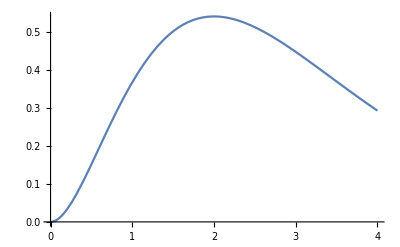

(a1 ⅇ^(-b1 p))/(b1 p)-(a2 ⅇ^(-b2 p))/(b2 p)

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{a1→1347.15,a2→1348.36,b1→0.242935,b2→0.24313}

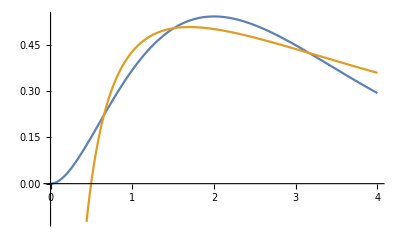

```mathematica
Clear[R0,alpha,b,p,y,a1,a2,b1,b2, alp,bet, w,t,s]

R0=8.58
a=1
alp = -2
bet = 1
w[p_,alpha_,b_] = Exp[-b*p]/(p/a)^(alpha);  
ug = 0.5
og = 4
                                                                      (* tempered Riesz FC *)
data = Table[{x,w[x,alp,bet]},{x,ug,og,0.01}];
Plot[w[x,alp,bet],{x,0,og}]

y[ p_, a1_,a2_,b1_,b2_] =a1 *Exp[-b1*p]/(b1*p)- a2 *Exp[-b2*p]/(b2*p); 
t = a1 *Exp[-b1*p]/(b1*p)- a2 *Exp[-b2*p]/(b2*p) 
s= FindFit[data,y[p,a1,a2,b1,b2],{a1,a2,b1,b2},p,MaxIterations->100000]
Plot[{w[p,alp,bet],t /. s},{p,0, og}]
```